# 0. Initial data

## 0.1 Dataset

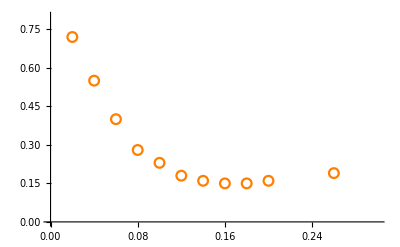

```mathematica
pairs = {{0.02,0.72},{0.04,0.55},{0.06,0.4},{0.08,0.28},{0.1,0.23},{0.12,0.18},{0.14,0.16},{0.16,0.15},{0.18,0.15},{0.2,0.16},{0.26,0.19}};
plotRange = {{0, 0.3}, {0, 0.8}};
size = 300;
dataDots = ListPlot[pairs, PlotStyle->Orange, PlotRange->plotRange, PlotMarkers->Graphics[Circle[],ImageSize->10]]
```

# 1. Interpolation

## 1.1 Local interpolation

#### 1.1.1 Built-in interpolation

InterpolatingFunction::dmval: Input value {6.12857×10^-6} lies outside the range of data in the interpolating function. Extrapolation will be used.

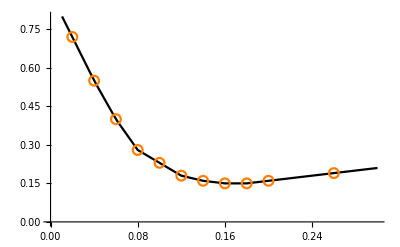

ММиАвАП\lab2\lin1.png

```mathematica
interp = Plot[Interpolation[pairs, InterpolationOrder->1][a], {a, 0, 0.3}, PlotStyle->Black, PlotRange->plotRange];
f2 = Show[interp, dataDots]
Export["ММиАвАП\\lab2\\lin1.png", f2]
```

#### 1.1.2 Self written interpolation

```mathematica
lines = {};
addLine[i_] := (
y1 = pairs[[i]][[2]];
y2 = pairs[[i + 1]][[2]];
x1 = pairs[[i]][[1]];
x2 = pairs[[i + 1]][[1]];
Module[{a, b}, 
a =  (y2 - y1) / (x2 - x1);
b =  y2 - x2 * a;
AppendTo[lines, Plot[a * x + b, {x, x1, x2}, PlotStyle->Black, PlotRange->plotRange]];
];
)
For[i = 1, i <= Length[pairs] - 1, i++,  addLine[i]]
```

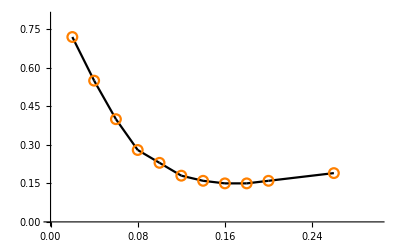

ММиАвАП\lab2\lin2.png

```mathematica
f3 = Show[{lines, dataDots}]
Export["ММиАвАП\\lab2\\lin2.png", f3]
```

## 1.2 Interpolation polynomial

#### 1.2.0 Local constants

```mathematica
polynomialRange = {{0, 0.3}, {-5, 0.8}};
```

#### 1.2.1 Built-in interpolation polynomial

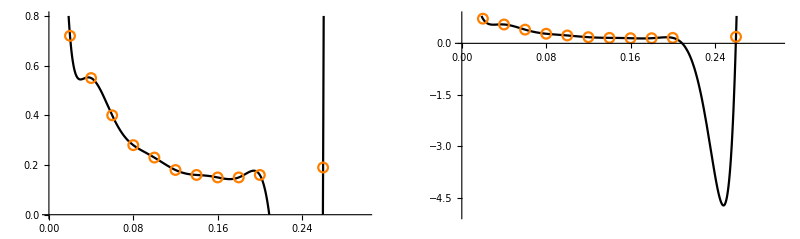

```mathematica
GraphicsRow[{
Show[Plot[InterpolatingPolynomial[pairs, x], {x, 0, 0.3}, PlotStyle->Black, PlotRange->plotRange], dataDots, ImageSize-> size], Show[Plot[InterpolatingPolynomial[pairs, x], {x, 0, 0.3}, PlotStyle->Black, PlotRange->polynomialRange], dataDots, ImageSize-> size]}]
```

#### 1.2.2 Self written interpolation polynomial

Polynomial

```mathematica
Polynomial = 0;

FormArg[xi_, xn_] := Function[(x - xn)/(xi  - xn)][x]

FormSummand[xi_, yi_]:= (
Summand = 1;
For[i = 1, i <= Length[pairs], i++,  (
tempX = pairs[[i]][[1]];
If[xi ≠ tempX, Summand *=  FormArg[xi, tempX]];
)];
Summand *= yi;
Polynomial += Summand;
)

Do[FormSummand[pairs[[i]][[1]], pairs[[i]][[2]]], {i, Length[pairs]}]
Polynomial
```

1.61469×10^10 (-0.26+x) (-0.2+x) (-0.18+x) (-0.16+x) (-0.14+x) (-0.12+x) (-0.1+x) (-0.08+x) (-0.06+x) (-0.04+x)-1.21102×10^11 (-0.26+x) (-0.2+x) (-0.18+x) (-0.16+x) (-0.14+x) (-0.12+x) (-0.1+x) (-0.08+x) (-0.06+x) (-0.02+x)+3.87525×10^11 (-0.26+x) (-0.2+x) (-0.18+x) (-0.16+x) (-0.14+x) (-0.12+x) (-0.1+x) (-0.08+x) (-0.04+x) (-0.02+x)-7.03286×10^11 (-0.26+x) (-0.2+x) (-0.18+x) (-0.16+x) (-0.14+x) (-0.12+x) (-0.1+x) (-0.06+x) (-0.04+x) (-0.02+x)+9.74867×10^11 (-0.26+x) (-0.2+x) (-0.18+x) (-0.16+x) (-0.14+x) (-0.12+x) (-0.08+x) (-0.06+x) (-0.04+x) (-0.02+x)-8.71931×10^11 (-0.26+x) (-0.2+x) (-0.18+x) (-0.16+x) (-0.14+x) (-0.1+x) (-0.08+x) (-0.06+x) (-0.04+x) (-0.02+x)+6.02816×10^11 (-0.26+x) (-0.2+x) (-0.18+x) (-0.16+x) (-0.12+x) (-0.1+x) (-0.08+x) (-0.06+x) (-0.04+x) (-0.02+x)-2.90644×10^11 (-0.26+x) (-0.2+x) (-0.18+x) (-0.14+x) (-0.12+x) (-0.1+x) (-0.08+x) (-0.06+x) (-0.04+x) (-0.02+x)+9.08261×10^10 (-0.26+x) (-0.2+x) (-0.16+x) (-0.14+x) (-0.12+x) (-0.1+x) (-0.08+x) (-0.06+x) (-0.04+x) (-0.02+x)-1.43528×10^10 (-0.26+x) (-0.18+x) (-0.16+x) (-0.14+x) (-0.12+x) (-0.1+x) (-0.08+x) (-0.06+x) (-0.04+x) (-0.02+x)+7.74723×10^7 (-0.2+x) (-0.18+x) (-0.16+x) (-0.14+x) (-0.12+x) (-0.1+x) (-0.08+x) (-0.06+x) (-0.04+x) (-0.02+x)

Plots

```mathematica
lagrange1 = Show[Plot[Polynomial, {x, 0, 0.3}, PlotStyle->Black, PlotRange->plotRange], dataDots];
lagrange2 = Show[Plot[Polynomial, {x, 0, 0.3}, PlotStyle->Black, PlotRange->polynomialRange], dataDots];
GraphicsRow[{lagrange1,lagrange2}]
Export["ММиАвАП\\lab2\\lagrange1.png", lagrange1];
Export["ММиАвАП\\lab2\\lagrange2.png", lagrange2];
```

-Graphics-

## 1.3 Spline

#### 1.3.1 Spline coefficients

{-21250.,1275.,-25.5,0.89}

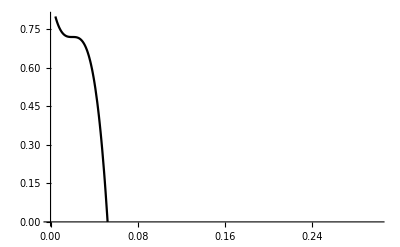

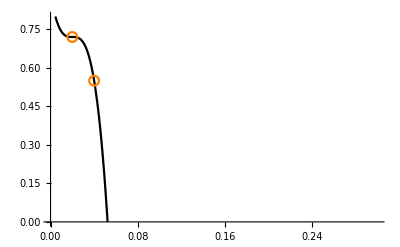

```mathematica
SplineCoeffs[d1_, d2_, x0_, y0_, x1_, y1_] := Module[{a = 0, b = 0, c= 0, d = 0},
a = ((y1 - y0)/(x1 - x0) - 0.5*d2*(x1-x0) - d1)/ Power[(x1 -x0), 2];
b = 0.5d2 - 3 * a * x0;
c = d1 - 3a*x0^2-2b*x0;
d = y0 - a*x0^3-b*x0^2 - c*x0;
{a, b, c, d}
]

spCoeff = SplineCoeffs[0 ,0, pairs[[1]][[1]], pairs[[1]][[2]], pairs[[2]][[1]], pairs[[2]][[2]] ]
spF = spCoeff[[1]]*x^3 +spCoeff[[2]]*x^2 +spCoeff[[3]]*x +spCoeff[[4]];
spplot = Plot[spF, {x, 0, 0.3}, PlotStyle->Black, PlotRange->plotRange]
Show[spplot, ListPlot[{{pairs[[1]][[1]], pairs[[1]][[2]]}, {pairs[[2]][[1]], pairs[[2]][[2]]}}, PlotStyle->Orange, PlotRange->plotRange, PlotMarkers->Graphics[Circle[],ImageSize->10]]]
Export["ММиАвАП\\lab2\\spplot.png", spplot];
```

# 2. Approximation

## 2.1 Standard deviation

```mathematica
Deviation[fn_] :=Module[{},
sum = 0;
For[i = 1, i <= Length[pairs], i++,  sum = sum + Power[fn[pairs[[i]][[1]]] - pairs[[i]][[2]], 2]];
δ = Sqrt[sum / (Length[pairs] + 1)];
Return[δ];
]
```

## 2.2 Linear approximation

#### 2.2.1 Polynomial of 1st order

FittedModel[0.541973-2.05272 x]

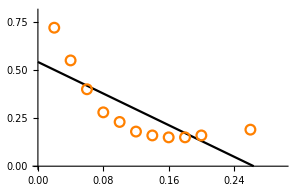

11

ММиАвАП\lab2\appr1.png

```mathematica
lm = LinearModelFit[pairs, x, x];
lm
appr1 = Show[Plot[lm[x], {x, 0, 0.3}, PlotStyle->Black, PlotRange->plotRange], dataDots, ImageSize-> size]
 Deviation[lm];
Export["ММиАвАП\\lab2\\appr1.png", appr1]
```

## 2.3 Nonlinear approximation

#### 2.3.1 Polynomial of 2nd order

FittedModel[0.813082-7.61501 x+20.6792 x^2]

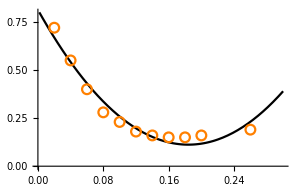

11

ММиАвАП\lab2\appr2.png

```mathematica
square=  LinearModelFit[pairs, {x^2, x, 1},  x];
square
appr2 = Show[Plot[square[x], {x, 0, 0.3}, PlotStyle->Black,PlotRange->plotRange], dataDots, ImageSize-> size]
Deviation[square];
Export["ММиАвАП\\lab2\\appr2.png", appr2]
```

#### 2.3.2 Polynomial of 3d order

FittedModel[0.951899-12.6952 x+64.5512 x^2-103.886 x^3]

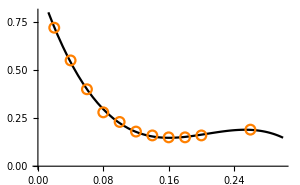

11

ММиАвАП\lab2\appr3.png

```mathematica
cubic =  LinearModelFit[pairs, {x^3, x^2, x, 1}, x];
cubic
appr3 = Show[Plot[cubic[x], {x, 0, 0.3}, PlotStyle->Black,PlotRange->plotRange], dataDots, ImageSize->size]
Deviation[cubic];
Export["ММиАвАП\\lab2\\appr3.png", appr3]
```

#### 2.3.3 Polynomial of 4th order

FittedModel[0.961845-13.2477 x+72.9739 x^2-150.783 x^3+85.1952 x^4]

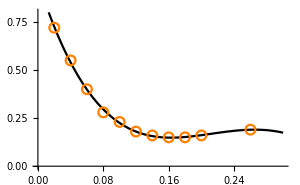

11

ММиАвАП\lab2\appr4.png

```mathematica
quad =  LinearModelFit[pairs, {x^4, x^3, x^2, x, 1}, x];
quad
appr4 = Show[Plot[quad[x], {x, 0, 0.3}, PlotStyle->Black,PlotRange->plotRange], dataDots, ImageSize->size]
Deviation[quad];
Export["ММиАвАП\\lab2\\appr4.png", appr4]
```

## 2.4 Normal equations

#### 2.4.1 Normal equations coefficients calculation

Polynomial order

```mathematica
polynomialOrder = 3;
```

X

```mathematica
XRow[matrix_, power_] := Module[{array = {}, x = {}},
Do[(
x = matrix[[i]][[1]];
AppendTo[array, Power[x, power]];
),{i, Length[matrix]}];
Return[Total[array]];
]

XMatrix[matrix_, power_] := Module[{array = {}},
array = Table[XRow[matrix, (i - 1) + (j - 1)],{i ,power + 1},{j, power + 1}];
Return[array];
]
```

Y

```mathematica
YRow[matrix_, power_] := Module[{array = {}, x = {}, y = {}},
Do[(
x = matrix[[i]][[1]];
y = matrix[[i]][[2]];
AppendTo[array, y * Power[x, power]];
),{i, Length[matrix]}];
Return[Total[array]];
]

YMatrix[matrix_, power_] := Module[{array = {}},
For[i = 0, i <= power, i++, AppendTo[array,YRow[matrix, i]]];
Return[array];
]
```

```mathematica
NormalEqCoeffs[matrix_] := Module[{m = {}, n = {}, result = {}},
m = XMatrix[matrix, polynomialOrder];
n =YMatrix[matrix, polynomialOrder];
result = LinearSolve[m, n];
Return[result];
];
```

#### 2.4.2 Approximation plot

Polynomial

```mathematica
FormPolynomialSummand[a_, power_] := Function[a * Power[x, power]][x];
FormPolynomial[coeffs_] := Do[normalPolynomial += FormPolynomialSummand[coeffs[[i]], i - 1], {i, Length[coeffs]}];
```

Plot

```mathematica
normalPolynomial = 0;
normCoeffs = NormalEqCoeffs[pairs];
Print[normCoeffs];
FormPolynomial[normCoeffs];
Print[normalPolynomial];
order3 = Show[Plot[normalPolynomial, {x, 0, 0.3}, PlotStyle->Black,PlotRange->plotRange], dataDots, ImageSize-> size]
Export["ММиАвАП\\lab2\\order3.png", order3]
```

{0.951899,-12.6952,64.5512,-103.886}

0.951899-12.6952 x+64.5512 x^2-103.886 x^3

-Graphics-

ММиАвАП\lab2\order3.png

## 2.5 Exponential approximation

#### 2.5.1 Exponential approximation

FittedModel[ⅇ^(0.0905904-20.7721 x+53.8199 x^2)]

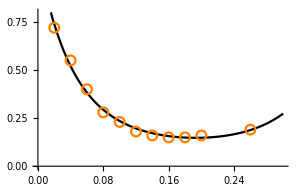

11

ММиАвАП\lab2\apprExp.png

```mathematica
exponentialAppr=  NonlinearModelFit[pairs, {Exp[a*x^2 + b*x + c]}, {a, b, c} , x];
exponentialAppr
apprExp = Show[Plot[exponentialAppr[x], {x, 0, 0.3}, PlotStyle->Black,PlotRange->plotRange], dataDots, ImageSize-> size]
Deviation[exponentialAppr];
Export["ММиАвАП\\lab2\\apprExp.png", apprExp]
```

## Comparison

{0.107286,0.0335726,0.00613099,0.00596578,0.0140355}

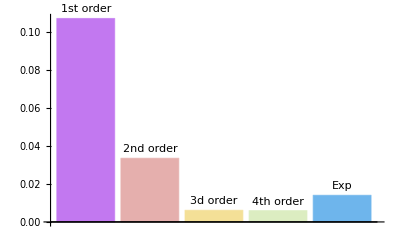

ММиАвАП\lab2\chart.png

```mathematica
dev = {Deviation[lm],Deviation[square], Deviation[cubic], Deviation[quad], Deviation[exponentialAppr]};
dev
chart  = BarChart[dev,ChartLabels-> Placed[{"1st order", "2nd order", "3d order", "4th order", "Exp"}, Above] , ChartStyle->"Pastel"]
Export["ММиАвАП\\lab2\\chart.png", chart]
```